```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
i=3
ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl1.dat"],{Real,Real,Real,Real,Real}];
Import[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl1.dat"]];
```

3

## Data Loss

```mathematica
count0=count1=count2=count3=0;
For[i=1,i≤dimdesc,i++,
count0+=Dimensions[ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_Meta3.edm"],metaStructure]][[1]];
count1+=Dimensions[ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_Meta5.dat"],metaStructure]][[1]];
count2+=Dimensions[ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl1.dat"],{Real,Real,Real,Real,Real}]][[1]];
count3+=
(Dimensions[ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],{Real,Real,Real,Real,Real,Real,Real,Real,Real}]][[1]]*9*2);
];
```

```mathematica
loss1=N[(count0-count1)]
loss2=N[(count1-count2)]
loss3=N[(count2-count3)]
clean1=count0-loss1-loss2-loss3;
tot1=clean1+loss1+loss3;
clean2=count0-loss1-loss3;
tot2=clean2+loss1+loss3;
PieChart[{{loss1,loss3,(tot2/4),clean1-(tot2/2)},{loss1,loss3,0,clean2}},ChartLegends->{"Unusable: No-n-Count = 48","Unusable: No-B-Field = 150","#{B_0} = 1189","Usable"},
TicksStyle->Directive[FontSize->40],Axes->None,AxesStyle->Thick,FrameStyle->Thick,LabelStyle->{22,Black,Bold},ImageSize->500,PlotLabel->"Total Cycles: 4756",
Epilog->{
Text[Style["A_(+/-)",FontSize->Large],{0.2,-.4}],
Text[Style["E_(0/(+/-))",FontSize->Large],{1.2,-1.2}]
}]
```

-Graphics-

## Level3: Averaging ABBA-BAAB patterns

```mathematica
rundat={};
starttime=0;
pta=pte=fta=fte=erra=erre={};
bpt10=bft10=errb10={};
bpt20=bft20=errb20={};
bpt0=bft0=errb0={};
pma=pme={};
pmarun=pmerun={};
pmb0run=pmbbrun={};
For[i=1,i≤dimdesc,i++,
pmarun=pmerun={};
pmb0run=pmbbrun={};
If[(descdat[[i]][[5]]>10)(*Accepting runs with > 10 cycles*)
,
Print[descdat[[i]][[4]]];
dimrundat=Dimensions[rundat][[1]];(*lvl2 run data: Cycle #, time stamp, B_0, U+D, Mon*)
If[i==1,starttime=rundat[[1]][[1]]];
(*A*)
pta=Join[pta,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{2,3}]]}]];
fta=Join[fta,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,2]]}]]; (*subtracting initial time so the first time stamp is 0 in the plot*)
erra=Join[erra,rundat[[;;,3]]];
pma=Join[pma,Table[PlusMinus[rundat[[k]][[2]],rundat[[k]][[3]]],{k,1,dimrundat}]];
pmarun=Join[pmarun,Table[PlusMinus[rundat[[k]][[2]],rundat[[k]][[3]]],{k,1,dimrundat}]];(*Accumulate all cycles with A-asymmetry*)
(*E*)
pte=Join[pte,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{4,5}]]}]];
fte=Join[fte,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,4]]}]];
erre=Join[erre,rundat[[;;,5]]];pme=Join[pme,Table[PlusMinus[rundat[[k]][[4]],rundat[[k]][[5]]],{k,1,dimrundat}]];
pmerun=Join[pmerun,Table[PlusMinus[rundat[[k]][[4]],rundat[[k]][[5]]],{k,1,dimrundat}]];(*Accumulate all cycles with E ratios*)
(*B*)
If[descdat[[i]][[6]]==10,{bpt10=Join[bpt10,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{8,9}]]}]];(*Selecting 10 muT cycles*)
bft10=Join[bft10,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,8]]}]];
errb10=Join[errb10,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
},
{bpt20=Join[bpt20,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{8,9}]]}]];(*Selecting 20 muT cycles*))
bft20=Join[bft20,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,8]]}]];
errb20=Join[errb20,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
}
];
bpt0=Join[bpt0,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,{6,7}]]}]];(*Selecting 0-zero muT cycles*)
bft0=Join[bft0,Transpose[{(rundat[[;;,1]]-starttime)/(24*3600),rundat[[;;,6]]}]];
errb0=Join[errb0,rundat[[;;,7]]];
pmb0run=Join[pmb0run,Table[PlusMinus[rundat[[k]][[6]],rundat[[k]][[7]]],{k,1,dimrundat}]];
];
Export[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],lvl3];
]
```

12693

12695

12697

12704

12707

12770

12771

12772

12773

12774

12775

12778

12779

12780

13099

13102

13103

13104

13106

13107

13108

13109

13110

13112

13132

13133

13134

13135

13136

13137

13138

13139

13140

13141

13142

13146

## First run, A: Fit all neutron counts in a run to PDF of Gaussian distribution, with : {width, central value, error on central value}.

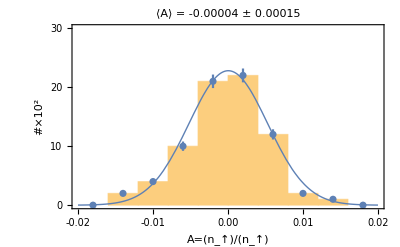

```mathematica
inset=Show[{
Histogram[hista,{-0.02,0.02,.004}, Frame->True,FrameLabel->{"A=(n_↑)/(n_↑)","#×10^2"},Axes->False,PlotRange->{{-.02,.02},{0,30}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},PlotLabel->"⟨A⟩ = -0.00004 ± 0.00015"],
EDAListPlot[{HistogramList[hista,{-0.02,0.02,.004}],HistogramList[hista,{-0.02,0.02,.004}],Fit[HistogramList[hista,{-0.02,0.02,.004}][[2]][[k]],PDF[NormalDistribution[pma[[1]],pma[[2]]]],{pma}]}(*Fitting histogram to width, central value, error on central value*)},{k,1,Dimensions[HistogramList[hista,{-0.02,0.02,.004}][[2]]][[1]]}]]
},ImageSize->{400}]
```

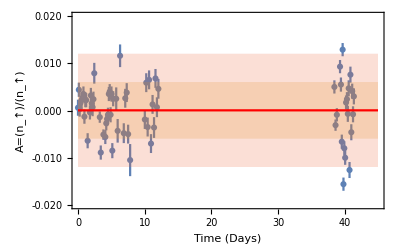

```mathematica
(***)
Show[{
EDAListPlot[pta,PlotRange->{{0,45},{-.02,0.02}},Frame->True,FrameLabel->{"Time (Days)","A=(n_↑)/(n_↑)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.002],ImageSize->{1600},Epilog->Inset[inset,{25,-.01}]]
}]
```

## E-1

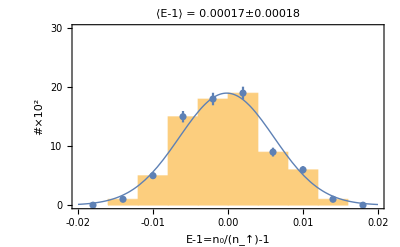

```mathematica
inset=Show[{
Histogram[histe,{-0.02,0.02,.004}, Frame->True,FrameLabel->{"E-1=n_0/(n_↑)-1","#×10^2"},Axes->False,PlotRange->{{-.02,.02},{0,30}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},PlotLabel->"⟨A⟩ = -0.00004 ± 0.00015"],
EDAListPlot[{HistogramList[histe,{-0.02,0.02,.004}],HistogramList[histe,{-0.02,0.02,.004}],Fit[HistogramList[histe,{-0.02,0.02,.004}][[2]][[k]],PDF[NormalDistribution[pme[[1]],pme[[2]]]],{pme}]}(*Fitting histogram to width, central value, error on central value*)},{k,1,Dimensions[HistogramList[histe,{-0.02,0.02,.004}][[2]]][[1]]}]]
},ImageSize->{400}]
```

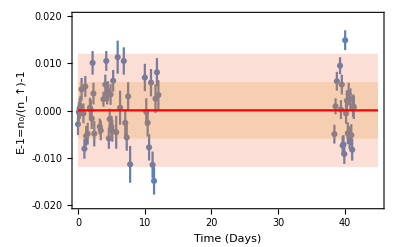

```mathematica
(***)
Show[{
EDAListPlot[pte,PlotRange->{{0,45},{-.02,0.02}},Frame->True,FrameLabel->{"Time (Days)","E-1=n_0/(n_↑)-1"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.002],ImageSize->{1600},Epilog->Inset[inset,{25,-.01}]]
}]
```

## B

```mathematica
(***)
Show[{
EDAListPlot[bpt0,bpt10,bpt20,PlotRange->{{0,45},{-.001,.025}},PlotStyle->{Gray,Blue,Red},Frame->True,FrameLabel->{"Time (Days)","B (mT)"},PlotLegends->{"B_0","|B_↑,_↓|=.01 mT","|B_↑,_↓|=.02 mT"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.002],ImageSize->{1000},PlotMarkers->{Automatic,Large}]
}]
```

-Graphics-